## Gambler’s problem

The states are
S={0,...,100}.
Actions are
A(s)={0,..,Min[s,100-s]}.

If the probability of heads is p_h, then
p(s',r|s,a)=(δ_(s'=100)δ_(r=1)+δ_(s'<100)δ_(r=0))(p_h δ_(s+a-s')+(1-p_h)δ_(s-a-s'))
and one can easily convince oneself that
𝔼[R_(t+1)+v_k(S_(t+1))|S_t=s,A_t=a]=p_h δ_(s+a=100)+(p_h v_k(s+a)+(1-p_h)v_k(s-a)).

### Value iteration

```mathematica
ValueIteration[ph_,θ_]:=Block[{V,Vhist,Δ=1.0+θ,v,Π},
V=ConstantArray[0.0,101];
Vhist={};
While[Δ>θ,
Δ=0.0;
Do[
v=V⟦s+1⟧;
V⟦s+1⟧=Max@Table[ph KroneckerDelta[s+a,100]+ph V⟦s+a+1⟧+(1-ph)V⟦s-a+1⟧,{a,Min[s,100-s]}];
Δ=Max[Δ,Abs[v-V⟦s+1⟧]]
,{s,1,99}
];
Vhist=Append[V⟦2;;-2⟧]@Vhist;
];
(* Find final policy. *)
Π=FindPolicy2[V,ph];
{V⟦2;;-2⟧,Π,Vhist}
]
```

In order to produce similar policy plots as in the book, state values must be rounded slightly and then breaking ties in favor of smaller stakes when argmaxing. This is done by ‘FindPolicy2’. The naive way with no rounding hackery is implemented by ‘FindPolicy1’.

```mathematica
FindPolicy1[V_,ph_]:=Table[First[Ordering[Table[ph KroneckerDelta[s+a,100]+ph V⟦s+a+1⟧+(1-ph)V⟦s-a+1⟧,{a,Min[s,100-s]}],-1]],{s,99}]
FindPolicy2[V_,ph_]:=Table[Min@Map[First]@MaximalBy[Round[Last[#],0.000001]&]@Thread[{Range[Min[s,100-s]],Table[ph KroneckerDelta[s+a,100]+ph V⟦s+a+1⟧+(1-ph)V⟦s-a+1⟧,{a,Min[s,100-s]}]}],{s,99}]
```

### p_h=0.4

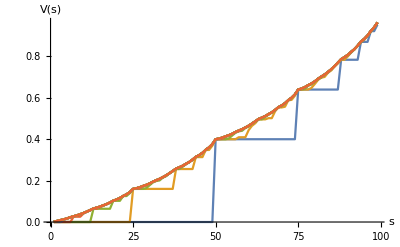

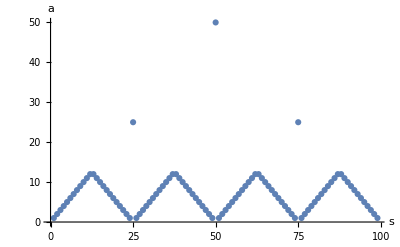

```mathematica
{V,Π,Vhist}=ValueIteration[0.4,10^-10];
ListLinePlot[Vhist,AxesLabel->{"s","V(s)"}]
ListPlot[Π,AxesLabel->{"s","a"},PlotRange->All]
```

### p_h=0.25

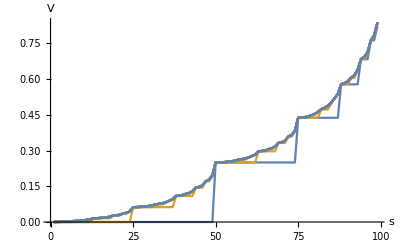

-Graphics-

```mathematica
{V,Π,Vhist}=ValueIteration[0.25,10^-10];
ListLinePlot[Vhist,AxesLabel->{"s","V"}]
ListPlot[Π,AxesLabel->{"s","a"},PlotRange->All]
```

### p_h=0.55

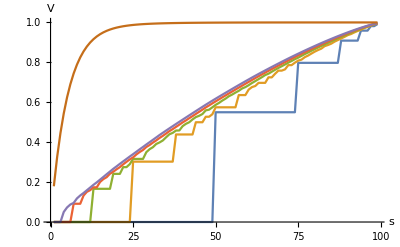

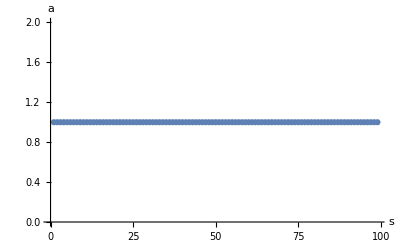

```mathematica
{V,Π,Vhist}=ValueIteration[0.55,10^-4];
ListLinePlot[Append[Last[Vhist]]@Take[Vhist,5],AxesLabel->{"s","V"}]
ListPlot[Π,AxesLabel->{"s","a"},PlotRange->All]
```